先生の結果と比べて自分の結果の１つ多い項の寄与を調べる

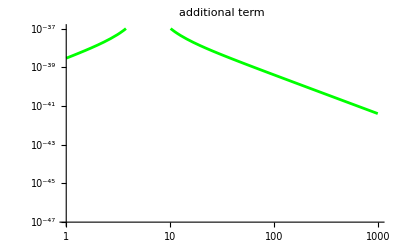

```mathematica
add=(4 kB T)/ω^2(ω s E0)/((M ω^2-s E0 k2 Cot[k2 L])^2)(χ ω)/((E0 s)^2+(χ ρ ω)^2)(α^2 T)/Cv 2(M ω^2)/(s E0)((s E0)^2-(χ ρ ω)^2)/.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
(*{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4};(*Sapphire*)*)
{kB->1.38 10^-23,T->300,α->3.9*10^(-7),L->0.602,κ->1.38*(0.0004 )^2 Pi/4,ρ->2.2*10^-3*(0.0004 )^2 Pi/4,Cv-> 7.7*10^2,ω->2π f,E0->7.2*10^10,M->40/4,s->(0.0004 )^2 Pi/4,χ->7.4*10^-8};(*fused silica*)
addg=LogLogPlot[add,{f,1,1000},PlotRange->{10^-47,10^-37},PlotStyle->{Green},PlotLabel->additional term]
```

自分の結果を書いたグラフ

4.48242×10^-21 √((-((8.18624×10^7-2.00242×10^-18 f^2) (-0.0872665 f^2+1.09831×10^-6 √(f^2) Cot[6.61183×10^-7 √(f^2)]))+(1.96378 √f (-0.0000256065 f (Sin[7844.87 √f]-Sinh[7844.87 √f])+(8.18624×10^7-2.00242×10^-18 f^2) (Sin[7844.87 √f]+Sinh[7844.87 √f])))/(-Cos[7844.87 √f]+Cosh[7844.87 √f]))/((8.18624×10^7+2.00242×10^-18 f^2) (40 f^2 π^2-0.00993728 √(f^2) Cot[6.61183×10^-7 √(f^2)])^2))

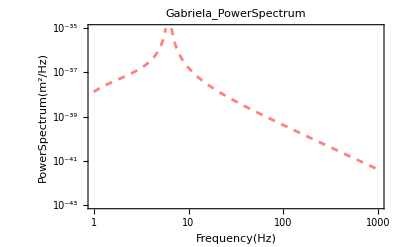

-Graphics-

-Graphics-

-Graphics-

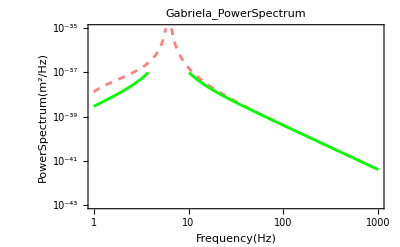

```mathematica
MyPS=(4 kB T)/ω^2(ω s E0)/((M ω^2-s E0 k2 Cot[k2 L])^2)(χ ω)/((E0 s)^2+(χ ρ ω)^2)(α^2 T)/Cv(√(ω/(2χ))1/(Cosh[2kd L] -Cos[2 kd L]) ((Sin[2 kd L]+Sinh[2 kd L])((s E0)^2-(χ ρ ω)^2) - (Sin[2 kd L] - Sinh[2 kd L])2 χ ρ ω s E0)-(k2 Cot[k2 L]-2(M ω^2)/(s E0))((s E0)^2-(χ ρ ω)^2)) /.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
(*{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};(*sapphire*)*)
{kB->1.38 10^-23,T->300,α->3.9*10^(-7),L->0.602,κ->1.38*(0.0004 )^2 Pi/4,ρ->2.2*10^-3*(0.0004 )^2 Pi/4,Cv-> 7.7*10^2,ω->2π f,E0->7.2*10^10,M->40/4,s->(0.0004 )^2 Pi/4,χ->7.4*10^-8};(*fused silica*)
GabSensi=√MyPS /200/3000

MyPSg=LogLogPlot[MyPS,{f,1,1000},PlotRange->{10^-43,10^-35},PlotStyle->{Pink,Dashed},PlotLabel->Gabriela_PowerSpectrum,Frame->True,FrameLabel->{Frequency[Hz],PowerSpectrum[m^2/Hz]}] (*my result*)
(*Sensitivity*)
GabSensiG=LogLogPlot[MySensi,{f,1,1000},PlotRange->{10^-27,10^-22},PlotLabel->Gabriela_Sensitivity,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}] 
(* Low Frequency*)
GabSensiG10=LogLogPlot[MySensi,{f,1,10},PlotRange->{10^-27,10^-22},PlotLabel->Gabriela_Sensitivity_LowFreq,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}] 
(* High Frequency*)
GabSensiG10=LogLogPlot[MySensi,{f,100,1000},PlotRange->{10^-27,10^-22},PlotLabel->Gabriela_Sensitivity_LowFreq,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}] 

Show[MyPSg,addg]
```

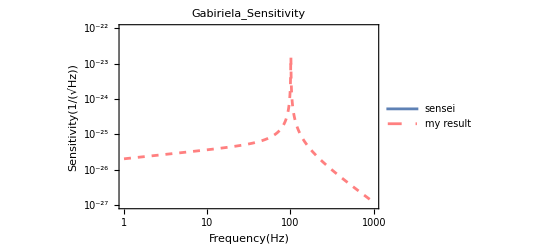

```mathematica
LogLogPlot[{Sensi,GabSensi},{f,1,1000},PlotRange->{10^-27,10^-22},PlotStyle->{Thick,{Pink,Dashed}},PlotLegends->Placed[{"sensei","my result"},{0.3,0.7}],PlotLabel->Gabiriela_Sensitivity,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]
```